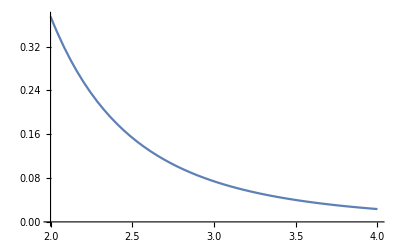

```mathematica
Plot[6/x^4,{x,2,4}]
```

```mathematica
ErrorT[x_]:=Abs[1/16(x-2)(x-2.75)(x-4)];
```

```mathematica
ErrorT[3.4]
```

0.034125

```mathematica
Pol[x_]:=(x-2)(x-2.75)(x-4);
```

```mathematica
PuntoCritico=Solve[D[Pol[x],x]==0,x];
```

```mathematica
PuntoCritico
```

{{x→2.33333},{x→3.5}}

```mathematica
Abs[Pol[2.3333333333333335]]
```

0.231481

```mathematica
Abs[Pol[3.5]]
```

0.5625